# Relaciones de Kramers Kronig sustractivas

```mathematica
(*En este código se obtiene la parte real del índice de refracción/función dieléctrica empleando las relaciones de Kramers-Kronig sustractivas, conociendo el valor de la parte imaginaria en algún punto *)
```

#### Modelo de Drude

```mathematica
omegaMin=0.5; (*valor mínimo de energía*)
omegaMax=10; (*valor máximo de energía*)
omega=Range[omegaMin,omegaMax,0.01]; (*rango de energías*)
omegaPAl=13.142; (*frecuencia de plasma Al*)
gammaAl=0.147; (*constante de amortuguamiento Al*)
```

```mathematica
(*Se define el modelo de drude*)
epsDrude[ω_,ωp_,γ_]:=1-((ωp)^2/(ω*(ω+ I γ)))
(*Se define la parte real y la imaginaria del índice de refracción*)
nImagDrude[energy_,omegaP_,gamma_]:=Im[Sqrt[epsDrude[energy,omegaP,gamma]]]
nReDrude[energy_,omegaP_,gamma_]:=Re[Sqrt[epsDrude[energy,omegaP,gamma]]]
```

```mathematica
alRealDrude=Table[{omega,nReDrude[omega,omegaPAl,gammaAl]},{omega,0.5,7,0.01}];
alImagDrude=Table[{omega,nImagDrude[omega,omegaPAl,gammaAl]},{omega,0.5,7,0.01}];
```

```mathematica
alReal1=nReDrude[3,omegaPAl,gammaAl];
omega1=3;
```

```mathematica
alReal1
```

0.110075

```mathematica
alRealDrude=Table[{w,nReDrude[w,omegaPAl,gammaAl]},{w,0.01,10,0.01}];
```

```mathematica
nReSSKK=Table[{w,
Re[alReal1+(2*(w^2-omega1^2)/Pi)*NIntegrate[nImagDrude[x,omegaPAl,gammaAl]*x/((x^2-w^2)*(x^2-omega1^2)),{x,0.01,10},Method->"PrincipalValue",Exclusions->{w,omega1}]]},{w,0.005,9.95,0.01}];
```

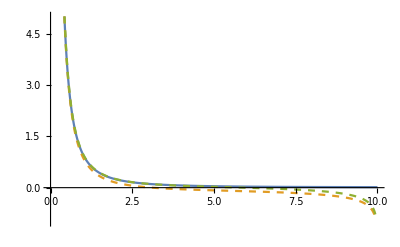

```mathematica
ListLinePlot[{alRealDrude,Style[nReKK,Dashed],Style[nReSSKK,Dashed]},PlotRange->{{0,10},{-1,5}}]
```

#### Valores experimentales del silicio

```mathematica
datos0=Import["C:\\Users\\Poh\\Documents\\GitHub\\Tesis-de-Licenciatura\\Programas\\ParteIm.csv"];
(*Se eliminan los encabezados de los datos*)
datos1=Drop[datos0,1];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Interpolation[Transpose[{datos1[[All,1]],datos1[[All,2]]}]];
(*Se toma a la primera columna como el vector de energía*)
omega=datos1[[All,1]];
```

```mathematica
parteReKK=Table[{w,1.+(2/Pi)*NIntegrate[parteIm[x]*x/(x^2-w^2),{x,0.5,w,6.},Method->"PrincipalValue"]},{w,omega[[2]],omega[[-2]],0.01}];
```

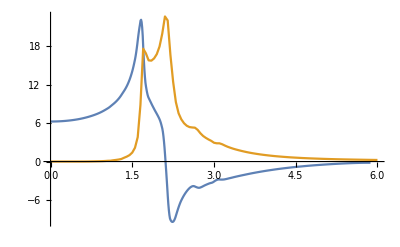

```mathematica
ListLinePlot[{parteReKK,parteIm}]
```

#### Datos experimentales del Oro

```mathematica
h=4.135667696*10^(-15); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ωAu=h c/λAu; (*eV*)
nau=Interpolation[Transpose[{ωAu,nau1[[All,2]]}],Method->"Spline"];
kAu=Interpolation[Transpose[{ωAu,kau1[[All,2]]}],Method->"Spline"];
```

```mathematica
nnau=Table[{w,nau[w]},{w,0.65,6.6,0.01}];
knau=Table[{w,kAu[w]},{w,0.65,6.6,0.01}];
```

```mathematica
nau[3]
ωAu[[-1]]
ωAu[[1]]
```

1.45997

0.640527

6.60298

```mathematica
omega1=4;
```

```mathematica
parteReAuSSKK=Table[{w,
Re[nau[4]+(2*(w^2-omega1^2)/Pi)*NIntegrate[kAu[x]*x/((x^2-w^2)*(x^2-omega1^2)),{x,0.6701,6.6},Method->"PrincipalValue",Exclusions->{w,omega1}]]},{w,0.66,6.5,0.01}];
```

NIntegrate::zeroregion: Integration region {{4.,3.9999999999999999854599716550434460691806830366765926909713193123}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.9999999999999915990590077442630758598992467152511567045477733351}. NIntegrate obtained 8.79815×10^14 and 3.11532×10^14 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{4.,4.0000000000000002652811643427282731800943910344318241045423695333}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.0000000000001532742134421757777744232369578970548039311555532649}. NIntegrate obtained 3.85229×10^14 and 4.09279×10^13 for the integral and error estimates.

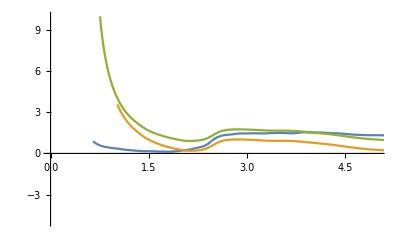

```mathematica
ListLinePlot[{nnau,parteReAuKK,parteReAuSSKK},PlotRange->{{0,5},{-5,10}}]
```

```mathematica
im287Erythrocytes=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
re287Erythrocytes=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
```

```mathematica
nErythrocytes1=Drop[re287Erythrocytes,1];
kErythrocytes1=Drop[im287Erythrocytes,1];
λErythrocytesRe=nErythrocytes1[[All,1]]; (*λ en nm*)
λErythrocytesIm=kErythrocytes1[[All,1]]; (*λ en nm*)
ωErythrocytesRe=h c/λErythrocytesRe; (*eV*)
ωErythrocytesIm=h c/λErythrocytesIm; (*eV*)
nErythrocytes=Interpolation[Transpose[{ωErythrocytesRe,nErythrocytes1[[All,2]]}]];
kErythrocytes=Interpolation[Transpose[{ωErythrocytesIm,kErythrocytes1[[All,2]]}]];
```

```mathematica
kErythrocytes[1.19]
```

0.0000810247

```mathematica
nErythrocytesPlot=Table[{w,nErythrocytes[w]},{w,1.19,4.82,0.01}];
kErythrocytesPlot=Table[{w,kErythrocytes[w]},{w,1.19,4.82,0.01}];
```

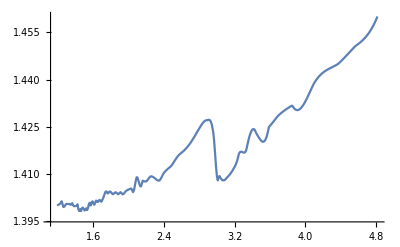

```mathematica
ListLinePlot[{nErythrocytesPlot},PlotRange->All]
```

```mathematica
omega1=3;
```

```mathematica
parteReAuSSKK=Table[{w,
Re[nErythrocytes[3]+(2*(w^2-omega1^2)/Pi)*NIntegrate[kErythrocytes[x]*x/((x^2-w^2)*(x^2-omega1^2)),{x,0.2,4.81},Method->"PrincipalValue",Exclusions->{w,omega1}]]},{w,1.19,4.82,0.01}];
```

NIntegrate::inumri: The integrand ((1.27-x) «1»)/((-16+(1.27-x)^2) (-1.6129+(1.27-x)^2))+((1.27+x) InterpolatingFunction[{{1.18329,4.84357}},{5,7,0,{62},{4},0,0,0,0,Automatic,«3»},{{1.18329,1.23241,«8»,«52»}},«1»,{Automatic}][1.27+x])/((-16+(1.27+x)^2) (-1.6129+(1.27+x)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,7.50713×10^-20}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{0.,7.5071275684497223727116419953998958159372743908937940578085924845×10^-20}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.0430437211093702291370933183150339933104606937604431068106757853×10^-15}. NIntegrate obtained 1.2424611150594612563776283717416044694730089172914147673943758001×10^-6 and 1.1453242155570083054954688053000024442482066280220364578056642416×10^-6 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{0.,3.145614326812469790228473237645125151142514187238399413709778239×10^-20}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.2750871540358150310614548934914821454637481745597889920643781475×10^-15}. NIntegrate obtained -0.00018608447595996003949202032926812214306974015420603633770835999151 and 0.000026371673769986453582112760592247165357638188897490341386816000418 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{4.,3.9999999999999999999999999999975469226433527539373491341972571313}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.8099999999818005269430007063403703861718095375482606712580491148}. NIntegrate obtained -0.00364759 and 6.49222×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::inumri: The integrand ((1.27-x) «1»)/((-16+(1.27-x)^2) (-1.6129+(1.27-x)^2))+((1.27+x) InterpolatingFunction[{{1.18329,4.84357}},{5,7,0,{62},{4},0,0,0,0,Automatic,«3»},{{1.18329,1.23241,«8»,«52»}},«1»,{Automatic}][1.27+x])/((-16+(1.27+x)^2) (-1.6129+(1.27+x)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,7.50713×10^-20}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{0.,7.5071275684497223727116419953998958159372743908937940578085924845×10^-20}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.0430437211093702291370933183150339933104606937604431068106757853×10^-15}. NIntegrate obtained 1.2424611150594612563776283717416044694730089172914147673943758001×10^-6 and 1.1453242155570083054954688053000024442482066280220364578056642416×10^-6 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{0.,3.145614326812469790228473237645125151142514187238399413709778239×10^-20}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.2750871540358150310614548934914821454637481745597889920643781475×10^-15}. NIntegrate obtained -0.00018608447595996003949202032926812214306974015420603633770835999151 and 0.000026371673769986453582112760592247165357638188897490341386816000418 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{0.,7.5071275684497223727116419953998958159372743908937940578085924845×10^-20}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.0430437211093702291370933183150339933104606937604431068106757853×10^-15}. NIntegrate obtained 1.2424611150594612563776283717416044694730089172914147673943758001×10^-6 and 1.1453242155570083054954688053000024442482066280220364578056642416×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

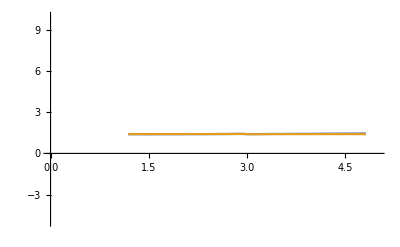

```mathematica
ListLinePlot[{nErythrocytesPlot,parteReAuSSKK},PlotRange->{{0,5},{-5,10}}]
```